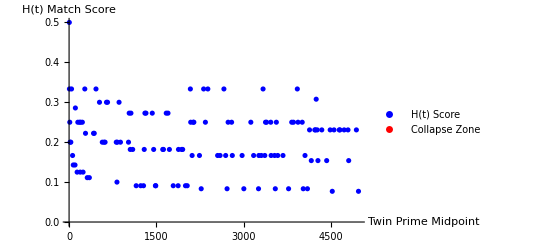

```mathematica
Module[{byte1Seed={1,4},byte1Seq,twinPrimes,isPrime,bbpDelta,limit=5000,n=3,hTarget=0.35,collapsePoints={},hScores={},hFunctionBase2},(*Byte1 sequence:extended recursion using binary-length deltas*)byte1Seq=NestList[Function[{pair},Module[{diff=Abs[pair[[-1]]-pair[[-2]]],len},len=IntegerLength[diff,2];
Append[pair,len]]],byte1Seed,300][[-1]];
(*Simple primality check*)isPrime[n_]:=PrimeQ[n];
(*BBP-modulated twin prime step function*)bbpDelta[n_]:=Floor[Total[Table[16^(1-k)/(8 k+Mod[n,7]+1),{k,1,4}]]]+1;
(*Generate twin primes with BBP skips*)twinPrimes=Reap[While[n<limit,If[isPrime[n]&&isPrime[n+2],Sow[{n,n+2}]];
n+=bbpDelta[n];]][[2,1]];
(*Define harmonic match score in base-2*)hFunctionBase2[tp_]:=Module[{digits,overlap,match},digits=IntegerDigits[tp[[1]],2];
overlap=Take[byte1Seq,Length[digits]];
match=Count[MapThread[Equal,{digits,overlap}],True];
N[match/Length[digits]]];
(*Score and detect collapse zones*)Do[Module[{h=hFunctionBase2[pair]},AppendTo[hScores,{Mean[pair],h}];
If[Abs[h-hTarget]<0.15,AppendTo[collapsePoints,{Mean[pair],1}]];],{pair,twinPrimes}];
(*Overlay all scores and collapse points*)Show[ListPlot[hScores,PlotStyle->Blue,AxesLabel->{"Twin Prime Midpoint","H(t) Match Score"},PlotLegends->{"H(t) Score"}],ListPlot[collapsePoints,PlotStyle->{Red,PointSize[Medium]},PlotLegends->{"Collapse Zone"}]]]
```